```mathematica
ClearAll["Global`*"]
```

# KMC testing calculations

## KMC 18-11-30 (Update needed)

Parameters

```mathematica
(* System parameters *)
dt = .0001; (* Time step *)
(* Crosslinker parameters *)
rcl = {0.0,0.0}; (* Position of crosslinker *)
hcl = 1.0; (* Crosslinker length *)
beta = 1.0 ;(* Inverse temp * boltz constant *)
kappa = 1.0; (* Spring constant of crosslinker *)
k0s = 1.0; (* Singly turnover rate of crosslinker *)
k0d = 1.0; (* Doubly turnover rate of crosslinker *)
eps = 1.0; (* Effective concentrations *)
Ka=1.0;(* Association constant *)
Ke=1.0;(* Equilibrium constant *)
rcut = .5; (* Cutoff distance *)
(* MT parameters*)
θ=0; (* Angle of MT *)
rmt = {0.0, 0.0}; (* Position of MT *)
Lmt = 20; (* Length of MT *)
mtu = {Cos[θ], Sin[θ]};
Dmt = 1.0;
lambda= 0.0;
```

Functions

```mathematica
getLen[y_, rc_]:=2*√(rc^2-y^2)
```

```mathematica
Prob01[l_]:=l*3/(4π*rcut^3)eps*k0s*dt (* l = MT length in cutoff sphere *)
```

```mathematica
Prob10 = k0s*dt;
```

```mathematica
Prob12[lim1_, lim2_, y_]:=dt*k0d*Ke*eps* NIntegrate[E^((-kappa*beta)/2*(1-lambda)*(√(x^2+y^2)-(hcl+Dmt))^2), {x, lim1, lim2}]
```

```mathematica
Prob21 =k0d*dt;
```

```mathematica
Pos01[lim1_, lim2_, roll_]:= (roll/Prob01[lim2-lim1])*(lim2-lim1)+lim1
```

```mathematica
Pos10[rv_, pos_, rc_]:={rc*(rv[[1]])^(1/3)*Sin[ArcCos[2*rv[[2]]-1]]*Cos[2π*rv[[3]]],rc*(rv[[1]])^(1/3)*Sin[ArcCos[2*rv[[2]]-1]]*Sin[2π*rv[[3]]], rc*(rv[[1]])^(1/3)*(2*rv[[2]]-1)}+pos
```

0 -> 1 calculations

```mathematica
(* Crosslinker in center of MT *)
Prob01[1]
```

0.000190986

```mathematica
0.0001909859317102744
```

0.000190986

```mathematica
(* Crosslinker outside of MT diameter*)
0
```

0

```mathematica
(* Crosslinker at tip of MT *)
Prob01[.5]
```

0.000095493

```mathematica
(* Crosslinker at surface of MT*)
0
```

0

```mathematica
(* Crosslinker between MT surface and radius*)
l = getLen[.25, rcut];
Prob01[l]
```

0.000165399

```mathematica
(* Crosslinker inside a MT smaller than 2*rcut *)
Prob01[.5]
```

0.000095493

## Multiple rods

```mathematica
(* Crosslinker between two semi overlapping MTs above their centers *)
l=getLen[.25, rcut];
Prob01[l]*2
```

0.000330797

```mathematica
(* Crosslinker between 4 semi overlapping MTs above their centers *)
l=getLen[.25, rcut];
Prob01[l]*4
```

0.000661595

### positions of binding

```mathematica
(* Position protein head is bound to with roll of .00001 and rcut of 1 *)
```

```mathematica
(.00001/Prob01[2])*2 -1
```

-0.94764

```mathematica
(.00007-Prob01[2])/Prob01[2]*2-1
```

-2.63348

```mathematica
(.00005/Prob01[getLen[.5,rcut]]*2-1)*.5*getLen[.5,rcut]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
((.00007-(Prob01[getLen[.5, rcut]]))/Prob01[getLen[.5,rcut]]*2-1)*.5*getLen[.5,rcut]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
((.00012-(2*Prob01[getLen[.5, rcut]]))/Prob01[getLen[.5,rcut]]*2-1)*.5*getLen[.5,rcut]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
Pos01[-10,-9.5,.00001]
```

-9.94764

```mathematica
Pos01[-10,-9.5,.00002-Prob01[.5]]
```

-10.3953

```mathematica
Prob01[.5]*5
```

0.000477465

```mathematica
Pos01[9.5,10,.00008-5*Prob01[.5]]
```

7.41888

1->0 calculations

```mathematica
(* Crosslinker bound in center *)
```

```mathematica
Prob10
```

0.0001

1->2 calculations

## Single rods (Calc12Prob)

```mathematica
(* Protein bound to center of one filament with unbound filament overlapping the first *)
Prob12[-10, 10, 0]
```

0.00048992

```mathematica
(* Parallel filaments separated vertically with one head bound to the center of another *)
Prob12[-10, 10, 1]
```

0.000548117

```mathematica
(* Parallel separated filaments with one head bound to the end plus of another *)
Prob12[-20, 0, 1]
```

0.000274058

```mathematica
(* Parallel overlapping filaments with one head bound to the minus end of another *)
Prob12[0, 20, 1]
```

0.000274058

```mathematica
(* Parallel inline rods with corsslinker bound at rod plus end and ohter rod shifted by rod lenght + D *)
Prob12[1, 21, 0]
```

0.000210894

```mathematica
(* Parallel rods with corsslinker bound at rod plus end and ohter rod shifted by rod lenght + D and vertically by D*)
Prob12[1, 21, 1]
```

0.000204685

```mathematica
(* Parallel filaments separated vertically with one head bound to the center of another *)
Prob12[-10, 10, 1]
```

0.000548117

```mathematica
(* EXTRAS *)
```

```mathematica
(* Protein bound and near rod of 0 length *)
0;
```

```mathematica
(* Protein bound with unbound rod tangent to rcut *)
```

```mathematica
0;
```

```mathematica
(* Protein bound with unbound rod outside of rcut *)
```

```mathematica
0;
```

```mathematica
(* Protein bound with unbound rod's closest end rcut away *)
```

```mathematica
0;
```

## Multiple rods (Calc12TotProbs)

```mathematica
(* No rods nearby *)
0;
```

```mathematica
(* 1 Rod nearby and above bound crosslinker *)
```

```mathematica
Prob12[-10, 10, 1]
```

0.000548117

```mathematica
(* 2 rods nearby, above and bellow *)
```

```mathematica
2*Prob12[-10, 10, 1]
```

0.00109623

```mathematica
(* 2 rods nearby, 1 perpendicular but same distance as other *)
```

```mathematica
2*Prob12[-10, 10, 1]
```

0.00109623

```mathematica
(* 2 rods above and below outside cutoff *)
```

```mathematica
0;
```

```mathematica
(* 2 rods touching cutoff *)
```

```mathematica
0;
```

```mathematica
(* 3 rods above and bellow, 2 are overlapping *)
```

```mathematica
3*Prob12[-10, 10, 1]
```

0.00164435

```mathematica
(* 3 rods above and bellow, 2 overlapping, 1 filtered *)
```

```mathematica
2*Prob12[-10, 10, 1]
```

0.00109623

```mathematica
(* 3 rods all completely inside rcut *)
```

```mathematica
2*Prob12[-1, 1, 1]+Prob12[-1, 1, 0]
```

0.000345628

```mathematica
(* 3 rods partially inside rcut with different angles *)
```

```mathematica
Prob12[0, 20, 1]+Prob12[0, 20, 0]+Prob12[1, 21, 0]
```

0.000729912

2->1 calculations

Cases

## 3 crossing perpendicular rods with protein in the center

### Unbound

```mathematica
(* Single rod binding probability *)
```

```mathematica
Prob01[1]
```

0.000190986

```mathematica
(* Total binding probability *)
```

```mathematica
Prob01[1]*3
```

0.000572958

#### Which rod to attach to and where

```mathematica
(* With a roll of .00001 *)
```

```mathematica
Pos01[-.5, .5, .00001]
```

-0.44764

```mathematica
-0.4476401224401701 (* Binds to rod 0 *)
```

-0.44764

```mathematica
(* With a roll of .00020 *)
roll = .0003 -Prob01[1]; (* Binds to rod 1 *)
Pos01[-.5, .5, roll]
```

0.0707963

```mathematica
(* With a roll of .9 *)
```

```mathematica
0 ;(* Doesn't bind to rod, returns -1 *)
```

### One head bound to first rod

#### 1 -> 0 unbinding

```mathematica
rollVec = {.1, .125, .125};
pos = {0, 0, 0};
```

```mathematica
(* Probability of unbinding *)
Prob10
```

0.0001

```mathematica
(* Where unbind *)
```

```mathematica
Pos10[rollVec, pos, rcut]
```

{0.108545,0.108545,-0.17406}

```mathematica
(* Change roll vector, where unbind *)
rollVec = {.1, 0, 0};
pos = {0, 0, 0};
Pos10[rollVec, pos, rcut]
```

{0.,0.,-0.232079}

#### 1 -> 2 binding

```mathematica
(* First rod binding prob *)
0 ;(* Head already bound to this rod *)
```

```mathematica
(* Second and third rod biding *)
Prob12[-10,10,0]
```

0.00048992

```mathematica
(* Total probability of binding *)
Prob12[-10,10,0]*2
```

0.000979841

### Two heads bound to first and second rod

```mathematica
(* Prob of first or second head unbinding *)
Prob21
```

0.0001

```mathematica
(* Location of unbound head = same as other bound head *)
{0,0,0}
```

{0,0,0}

## 4 parallel rods separated perpendicularly by half a rod diameter with protein in the center

### Unbound

```mathematica
(* Probability of binding to any one of the 4 rods *)
l=getLen[.25,.5];
Prob01[l]
```

0.000165399

```mathematica
(* Total binding probability *)
Prob01[l]*4
```

0.000661595

#### Placement of head

```mathematica
(* Position when binding to first rod, roll=.00005 *)
roll = .00005;
lim=getLen[.25,.5]/2;
Pos01[-lim,lim,roll]
```

-0.171213

```mathematica
(* Position when binding to second rod, roll=.0002 *)
l=getLen[.25,.5];
roll = .0002-Prob01[l];
lim=getLen[.25,.5]/2;
Pos01[-lim,lim,roll]
```

-0.251841

```mathematica
(* Position when binding to third rod, roll=.00035 *)
l=getLen[.25,.5];
roll = .00035-Prob01[l];
lim=getLen[.25,.5]/2;
Pos01[-lim,lim,roll]
```

0.533558

```mathematica
(* Position when not unbinding, roll=.1 *)
(* no change, return rod -1*)
```

### One head bound to first rod

```mathematica
(* Probability of unbinding *)
Prob10
```

0.0001

#### 1 -> 0 unbinding

```mathematica
rollVec = {.1, .125, .125};
pos = {0, .25, 0};
```

```mathematica
(* Where unbind *)
```

```mathematica
Pos10[rollVec, pos, rcut]
```

{0.108545,0.358545,-0.17406}

```mathematica
(* Change roll vector, where unbind *)
rollVec = {.1, 0, 0};
pos = {0, .25, 0};
Pos10[rollVec, pos, rcut]
```

{0.,0.25,-0.232079}

#### 1 -> 2 binding

```mathematica
(* Minimum distance to second rod *)
.5
```

0.5

```mathematica
(* Minimum distance to third and forth rod *)
.25*√2
```

0.353553

```mathematica
(* First rod binding prob *)
0 ;(* Head already bound to this rod *)
```

```mathematica
(* Second rod binding *)
p2 = Prob12[-10,10,.5]
```

0.000511748

```mathematica
(* Third and fourth rod binding *)
p3 = Prob12[-10,10,.25*√2]
```

0.000502191

```mathematica
(* Total binding probability *)
p2+2*p3
```

0.00151613

### Two heads bound to first and second rod

```mathematica
(* Prob of first or second head unbinding *)
Prob21
```

0.0001

```mathematica
(* Location of unbound head = same as other bound head *)
{0,.25,0}
```

{0,0.25,0}

## 6 perpendicular rods surrounding a sphere with a radius of half a rod diameter with protein in the center

### Unbound

```mathematica
(* Probability of binding to any one of the 6 rods *)
Prob01[.25]
```

0.0000477465

```mathematica
(* Total binding probability *)
Prob01[.25]*6
```

0.000286479

#### Placement of head

```mathematica
(* Position when binding to first rod, roll=.00001 *)
roll = .00001;
Pos01[-10,-9.75,roll]
```

-9.94764

```mathematica
(* Position when binding to second rod, roll=.00005 *)
roll = .00005-Prob01[.25];
Pos01[-10,-9.75,roll]
```

-9.9882

```mathematica
(* Position when binding to third rod, roll=.00028 *)
roll = .00028-5*Prob01[.25];
Pos01[9.75,10, roll]
```

9.96608

```mathematica
(* Position when not unbinding, roll=.1 *)
(* no change, return rod -1*)
```

### One head bound to first rod

```mathematica
(* Probability of unbinding *)
Prob10
```

0.0001

#### 1 -> 0 unbinding

```mathematica
rollVec = {.1, .125, .125};
pos = {.25, 0, 0};
```

```mathematica
(* Where unbind *)
```

```mathematica
Pos10[rollVec, pos, rcut]
```

{0.358545,0.108545,-0.17406}

```mathematica
(* Change roll vector, where unbind *)
rollVec = {.1, 0, 0};
Pos10[rollVec, pos, rcut]
```

{0.25,0.,-0.232079}

#### 1 -> 2 binding

```mathematica
(* Minimum distance to second rod *)
.5
```

0.5

```mathematica
(* Minimum distance to third, forth, fifth, and sixth rod *)
.25*√2
```

0.353553

```mathematica
(* First rod binding prob *)
0 ;(* Head already bound to this rod *)
```

```mathematica
(* Second rod binding *)
p2 = Prob12[.5,20.5,0]
```

0.000233917

```mathematica
(* Rest of rods binding *)
p3 = Prob12[.25,20.25,.25]
```

0.000242572

```mathematica
(* Total binding probability *)
p2+4*p3
```

0.00120421

### Two heads bound to first and second rod

```mathematica
(* Prob of first or second head unbinding *)
Prob21
```

0.0001

```mathematica
(* Location of unbound head = same as other bound head *)
{.25,0,0}
```

{0.25,0,0}

## Force-dependent detachment lookup tables

Parameters

```mathematica
(* Crosslinker parameters *)
distPerp = 0.; (* Distance perpendicular to filament *)
freelength = .05; (* Crosslinker rest length *)
beta =  1./.00411;(* Inverse temp * boltz constant *)
kappa = .1*1.0; (* Spring constant of crosslinker *)
lambda= 0.5;
xc = .005;(* force dependent characteristic length *)
(* MT parameters*)
Dmt = .024;
(* Error tolerance *)
small = .0001;
```

Functions

```mathematica
getSbound[κ_, β_, ℓ_, λ_,xc_, ϵ_]:= (xc+√(xc^2-(2(1-λ)Log[ϵ])/(β κ)))/(1-λ)+ℓ
```

```mathematica
getLen[y_, rc_]:=2*√(rc^2-y^2)
```

```mathematica
FdepProb12[lim1_, lim2_, y_]:= NIntegrate[E^(-kappa*beta*(1/2(1-lambda)*(√(x^2+y^2)-freelength)^2-xc(√(x^2+y^2)-freelength))), {x, lim1, lim2}]
```

```mathematica
FdepProb12Full[lim1_, lim2_, y_,M_, ℓ_, λ_,xc_]:= NIntegrate[E^(-M*(1/2(1-λ)*(√(x^2+y^2)-ℓ)^2-xc(√(x^2+y^2)-ℓ))), {x, lim1, lim2}]
```

Sbound tests

```mathematica
getSbound[.1*kappa,beta, freelength, lambda,xc, small]
getSbound[kappa,beta, freelength, lambda,xc, small]
getSbound[10*kappa,beta, freelength, lambda,xc, small]
```

3.95126

1.29056

0.449253

Lookup tests

```mathematica
s = getSbound[kappa,beta, freelength, lambda,xc, small]
FdepProb12[0, s*.9, 0.06]
```

1.29056

0.413951

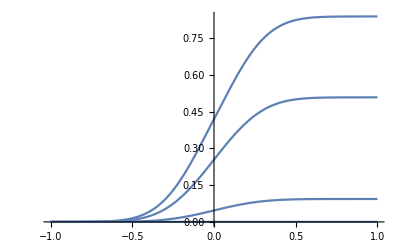

```mathematica
Plot[Table[FdepProb12[-s,s*x,i],{i,{0, .25*s, .5*s,s}}],{x,-1,1}]
```

```mathematica
Table[FdepProb12[0,s,i],{i,{0,.01,.05,.1,.5,1.}}]
```

{0.419145,0.419065,0.415718,0.403232,0.116774,0.00171489}

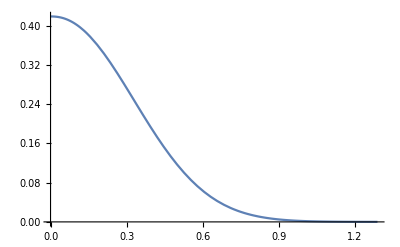

```mathematica
Plot[FdepProb12[0,s,i],{i,0,s}]
```

```mathematica
Manipulate[Plot[E^(-kappa*beta*(1/2(1-lambda)*(√(x^2+y^2)-freelength)^2-xc(√(x^2+y^2)-freelength))),{x,-s,s}],{y,0,s},{xc,0,.1},{lambda,0,1},{freelength,0,.1},{kappa,.1,10}]
```

General::munfl: Exp[-720.758] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-742.682] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-742.412] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-789.096] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-775.351] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-898.096] is too small to represent as a normalized machine number; precision may be lost.